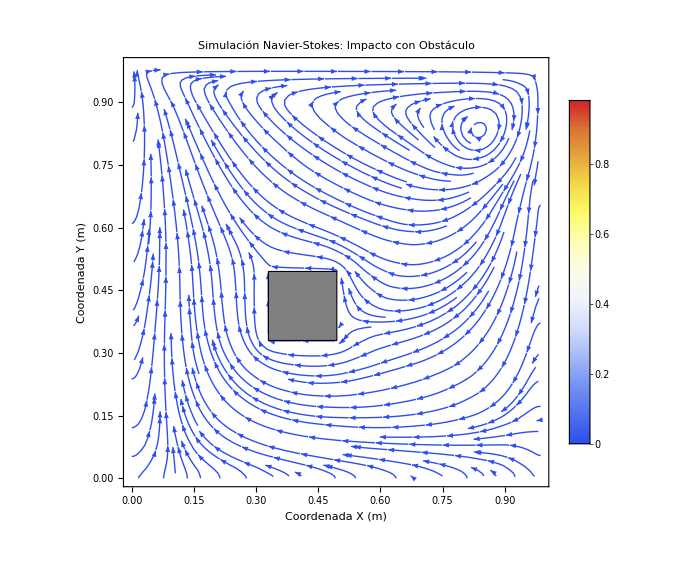

```mathematica
(*1. Importar los datos*)SetDirectory[NotebookDirectory[]];
datosCrudos=Import["resultado_fluido.csv","CSV"];
datosSinEncabezado=Rest[datosCrudos];

(*2. Formatear para ListStreamPlot*)
datosFormateados=Map[{{#[[1]],#[[2]]},{#[[3]],#[[4]]}}&,datosSinEncabezado];

(*3. Definir las coordenadas del obstáculo en metros*)
xMin=0.33;
xMax=0.495;
yMin=0.33;
yMax=0.495;

(*4. Generar la gráfica con el bloque superpuesto*)
graficaObstaculo=ListStreamPlot[datosFormateados,StreamColorFunction->"TemperatureMap",StreamPoints->Fine,PlotLegends->Automatic,FrameLabel->{Style["Coordenada X (m)",Black,14,Bold],Style["Coordenada Y (m)",Black,14,Bold]},PlotLabel->Style["Simulación Navier-Stokes: Impacto con Obstáculo",Black,Bold,16],LabelStyle->Directive[Black,12],ImageSize->Large,Background->White,ImagePadding->{{60,20},{60,40}},(*EPILOG:Dibujamos el bloque encima de la gráfica*)Epilog->{Gray,(*Color de relleno*)EdgeForm[Black],(*Borde negro para que resalte*)Rectangle[{xMin,yMin},{xMax,yMax}] (*Coordenadas {esquina inferior izquierda,esquina superior derecha}*)}]
```